```mathematica
FullForm[Plot[Sin[x], {x, 0, 10}]]/.Graphics[x__]:>x
```

FullForm::optx: Unknown option DisplayFunction in FullForm[{{{{},{},{Directive[Opacity[«1»],RGBColor[«3»],AbsoluteThickness[«1»]],Line[{«565»}]}}},{},{}},{DisplayFunction→Identity,Ticks→{Automatic,Automatic},AxesOrigin→{0,0},«19»,PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},Ticks→{Automatic,Automatic}}].

FullForm[{{{{},{},{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Line[{{2.04082×10^-7,2.04082×10^-7},{0.00306718,0.00306717},{0.00613415,0.00613412},{0.0122681,0.0122678},{0.024536,0.0245335},{0.0490718,0.0490521},{0.0981434,0.0979859},{0.196287,0.195029},{0.409084,0.397769},{0.607779,0.571045},{0.610823,0.573541},{0.613866,0.576032},{0.619954,0.580997},{0.632129,0.590863},{0.656478,0.610331},{0.705178,0.648169},{0.802576,0.719149},{0.805878,0.721439},{0.80918,0.723721},{0.815783,0.728263},{0.82899,0.737249},{0.855404,0.754836},{0.908231,0.788417},{0.911532,0.790443},{0.914834,0.792461},{0.921437,0.796472},{0.934644,0.804388},{0.961058,0.819798},{1.01388,0.848892},{1.01697,0.850516},{1.02005,0.852133},{1.02621,0.855342},{1.03854,0.861662},{1.06319,0.873909},{1.11249,0.896802},{1.11557,0.898161},{1.11865,0.899512},{1.12481,0.902187},{1.13714,0.907435},{1.16179,0.917516},{1.21109,0.936001},{1.21443,0.937171},{1.21777,0.938331},{1.22445,0.940619},{1.23781,0.945069},{1.26452,0.953463},{1.26786,0.954465},{1.2712,0.955455},{1.27788,0.957405},{1.29124,0.961177},{1.31795,0.968204},{1.32129,0.969034},{1.32463,0.969853},{1.33131,0.971459},{1.34466,0.974541},{1.348,0.975284},{1.35134,0.976017},{1.35802,0.977449},{1.37138,0.980182},{1.37472,0.980838},{1.37806,0.981483},{1.38474,0.982741},{1.39809,0.985124},{1.40143,0.985692},{1.40477,0.98625},{1.41145,0.987331},{1.42481,0.989363},{1.42809,0.989834},{1.43137,0.990295},{1.43792,0.991185},{1.45104,0.992837},{1.45431,0.993224},{1.45759,0.993599},{1.46415,0.994319},{1.47726,0.995629},{1.48054,0.99593},{1.48382,0.99622},{1.49038,0.996768},{1.49366,0.997026},{1.49693,0.997273},{1.50349,0.997736},{1.50677,0.997951},{1.51005,0.998155},{1.51333,0.998349},{1.5166,0.998532},{1.51988,0.998704},{1.52316,0.998866},{1.52972,0.999156},{1.533,0.999286},{1.53627,0.999404},{1.53955,0.999512},{1.54283,0.999609},{1.54611,0.999695},{1.54939,0.999771},{1.55267,0.999836},{1.55595,0.99989},{1.55922,0.999933},{1.5625,0.999966},{1.56578,0.999987},{1.56906,0.999998},{1.57234,0.999999},{1.57562,0.999988},{1.57889,0.999967},{1.58217,0.999935},{1.58545,0.999893},{1.58873,0.999839},{1.59201,0.999775},{1.59529,0.9997},{1.59856,0.999614},{1.60184,0.999518},{1.60512,0.999411},{1.6084,0.999293},{1.61168,0.999164},{1.61496,0.999025},{1.61824,0.998875},{1.62151,0.998714},{1.62479,0.998543},{1.62807,0.99836},{1.63463,0.997963},{1.63769,0.997764},{1.64074,0.997555},{1.64686,0.997109},{1.64992,0.996872},{1.65298,0.996625},{1.65909,0.996104},{1.66215,0.99583},{1.66521,0.995546},{1.67132,0.994951},{1.68356,0.993649},{1.68662,0.9933},{1.68967,0.992942},{1.69579,0.992199},{1.70802,0.990599},{1.71108,0.990176},{1.71414,0.989744},{1.72025,0.988852},{1.73249,0.986957},{1.73554,0.98646},{1.7386,0.985954},{1.74472,0.984914},{1.75695,0.982723},{1.78142,0.977902},{1.78447,0.977258},{1.78753,0.976605},{1.79365,0.975271},{1.80588,0.972495},{1.83035,0.966506},{1.83366,0.965649},{1.83698,0.964782},{1.84361,0.963017},{1.85687,0.959358},{1.8834,0.951535},{1.88672,0.95051},{1.89003,0.949475},{1.89667,0.947372},{1.90993,0.943043},{1.93646,0.933887},{1.93978,0.932696},{1.94309,0.931495},{1.94972,0.929062},{1.96299,0.924074},{1.98952,0.91361},{2.04257,0.890762},{2.04567,0.889351},{2.04877,0.887931},{2.05496,0.885066},{2.06734,0.879235},{2.09211,0.867168},{2.14164,0.841447},{2.2407,0.783881},{2.24374,0.781993},{2.24677,0.780098},{2.25284,0.776286},{2.26498,0.768577},{2.28926,0.752819},{2.33781,0.719983},{2.43493,0.6493},{2.64567,0.475844},{2.84231,0.294838},{3.05546,0.086031},{3.26471,-0.122803},{3.45986,-0.312917},{3.67151,-0.505466},{3.6746,-0.508127},{3.67769,-0.510783},{3.68386,-0.516081},{3.69621,-0.526618},{3.7209,-0.547448},{3.77029,-0.588095},{3.86907,-0.66499},{3.87242,-0.667484},{3.87576,-0.669971},{3.88245,-0.674922},{3.89583,-0.684734},{3.92259,-0.703988},{3.97611,-0.74097},{3.97945,-0.743212},{3.9828,-0.745446},{3.98949,-0.749889},{4.00287,-0.758672},{4.02962,-0.775831},{4.08314,-0.80847},{4.08643,-0.810399},{4.08971,-0.812318},{4.09628,-0.816131},{4.10941,-0.823651},{4.13568,-0.838264},{4.18823,-0.865743},{4.19151,-0.867382},{4.19479,-0.869012},{4.20136,-0.872243},{4.2145,-0.878592},{4.24077,-0.890834},{4.29331,-0.913465},{4.29638,-0.914707},{4.29944,-0.915941},{4.30557,-0.918383},{4.31782,-0.923163},{4.34233,-0.932306},{4.34539,-0.933409},{4.34846,-0.934504},{4.35458,-0.936668},{4.36684,-0.940889},{4.39135,-0.948907},{4.39441,-0.949869},{4.39747,-0.950823},{4.4036,-0.952703},{4.41586,-0.956355},{4.44036,-0.963229},{4.44343,-0.964047},{4.44649,-0.964857},{4.45262,-0.966449},{4.46487,-0.969524},{4.48938,-0.975237},{4.4927,-0.975966},{4.49602,-0.976684},{4.50267,-0.978089},{4.51595,-0.980769},{4.51928,-0.981411},{4.5226,-0.982043},{4.52924,-0.983275},{4.54253,-0.985608},{4.54585,-0.986164},{4.54917,-0.986709},{4.55581,-0.987767},{4.5691,-0.989752},{4.57242,-0.99022},{4.57574,-0.990678},{4.58238,-0.991561},{4.59567,-0.993196},{4.59899,-0.993578},{4.60231,-0.993948},{4.60896,-0.994656},{4.61228,-0.994993},{4.6156,-0.99532},{4.62224,-0.99594},{4.62557,-0.996233},{4.62889,-0.996516},{4.63553,-0.997048},{4.63885,-0.997297},{4.64217,-0.997536},{4.64882,-0.99798},{4.65214,-0.998185},{4.65546,-0.99838},{4.65878,-0.998563},{4.6621,-0.998736},{4.66542,-0.998897},{4.66875,-0.999048},{4.67207,-0.999187},{4.67539,-0.999316},{4.67871,-0.999433},{4.68203,-0.999539},{4.68535,-0.999635},{4.68867,-0.999719},{4.692,-0.999792},{4.69532,-0.999854},{4.69864,-0.999905},{4.70196,-0.999946},{4.70506,-0.999973},{4.70816,-0.999991},{4.71126,-0.999999},{4.71437,-0.999998},{4.71747,-0.999987},{4.72057,-0.999967},{4.72367,-0.999936},{4.72677,-0.999897},{4.72987,-0.999847},{4.73297,-0.999788},{4.73607,-0.99972},{4.73918,-0.999641},{4.74228,-0.999553},{4.74538,-0.999456},{4.74848,-0.999349},{4.75158,-0.999232},{4.75468,-0.999106},{4.75778,-0.99897},{4.76399,-0.998669},{4.76709,-0.998504},{4.77019,-0.99833},{4.77639,-0.997953},{4.77949,-0.997749},{4.78259,-0.997537},{4.7888,-0.997082},{4.8012,-0.996059},{4.8043,-0.995779},{4.8074,-0.99549},{4.8136,-0.994882},{4.82601,-0.993552},{4.82911,-0.993196},{4.83221,-0.99283},{4.83841,-0.992069},{4.85082,-0.990434},{4.85392,-0.990001},{4.85702,-0.989559},{4.86322,-0.988646},{4.87563,-0.986706},{4.90044,-0.982371},{4.90348,-0.981798},{4.90652,-0.981216},{4.9126,-0.980025},{4.92476,-0.977534},{4.94908,-0.972118},{4.95212,-0.971401},{4.95516,-0.970674},{4.96125,-0.969195},{4.97341,-0.966128},{4.99773,-0.959566},{5.00077,-0.958706},{5.00381,-0.957837},{5.00989,-0.956072},{5.02205,-0.952436},{5.04637,-0.944743},{5.09502,-0.927686},{5.09832,-0.926449},{5.10162,-0.925203},{5.10821,-0.922679},{5.12141,-0.917512},{5.14779,-0.9067},{5.20057,-0.88319},{5.20386,-0.881638},{5.20716,-0.880077},{5.21376,-0.876925},{5.22695,-0.870508},{5.25334,-0.85722},{5.30611,-0.828864},{5.30919,-0.827139},{5.31227,-0.825405},{5.31842,-0.821914},{5.33073,-0.814839},{5.35536,-0.800319},{5.40461,-0.769833},{5.5031,-0.70334},{5.50644,-0.700965},{5.50977,-0.698582},{5.51644,-0.693792},{5.52979,-0.684121},{5.55647,-0.664415},{5.60985,-0.623597},{5.7166,-0.536754},{5.9262,-0.349449},{6.1217,-0.160782},{6.33371,0.0505068},{6.53162,0.24589},{6.72563,0.428154},{6.93616,0.60755},{6.93923,0.609984},{6.9423,0.612413},{6.94843,0.617254},{6.96071,0.626866},{6.98526,0.645805},{7.03437,0.682503},{7.03744,0.684743},{7.04051,0.686977},{7.04664,0.691424},{7.05892,0.700241},{7.08347,0.717556},{7.13258,0.750879},{7.1359,0.753072},{7.13923,0.755257},{7.14589,0.759602},{7.15919,0.76819},{7.18581,0.784956},{7.23904,0.816809},{7.24237,0.818724},{7.2457,0.82063},{7.25235,0.824414},{7.26566,0.831873},{7.29228,0.846348},{7.34551,0.873489},{7.34862,0.874997},{7.35172,0.876497},{7.35794,0.879471},{7.37036,0.885318},{7.39522,0.8966},{7.39832,0.897971},{7.40143,0.899334},{7.40764,0.902034},{7.42007,0.907328},{7.44492,0.917496},{7.44803,0.918727},{7.45114,0.91995},{7.45735,0.922368},{7.46978,0.927097},{7.49463,0.936125},{7.54434,0.952442},{7.54738,0.953366},{7.55043,0.954281},{7.55652,0.956084},{7.5687,0.959584},{7.59307,0.966156},{7.59612,0.966937},{7.59916,0.967709},{7.60525,0.969227},{7.61744,0.972154},{7.6418,0.977575},{7.64485,0.978212},{7.6479,0.978839},{7.65399,0.980068},{7.66617,0.982415},{7.66922,0.982979},{7.67226,0.983534},{7.67835,0.984617},{7.69054,0.986673},{7.69358,0.987164},{7.69663,0.987646},{7.70272,0.988582},{7.7149,0.990344},{7.71795,0.990762},{7.721,0.99117},{7.72709,0.99196},{7.73927,0.993428},{7.74257,0.993801},{7.74588,0.994162},{7.75249,0.994854},{7.75579,0.995183},{7.75909,0.995501},{7.7657,0.996106},{7.769,0.996392},{7.77231,0.996667},{7.77892,0.997184},{7.78222,0.997426},{7.78552,0.997658},{7.79213,0.998088},{7.79543,0.998287},{7.79874,0.998474},{7.80204,0.998651},{7.80535,0.998818},{7.80865,0.998973},{7.81195,0.999117},{7.81526,0.99925},{7.81856,0.999373},{7.82187,0.999484},{7.82517,0.999585},{7.82847,0.999675},{7.83178,0.999753},{7.83508,0.999821},{7.83838,0.999878},{7.84169,0.999924},{7.84499,0.99996},{7.8483,0.999984},{7.8516,0.999997},{7.8549,1.},{7.85821,0.999991},{7.86151,0.999972},{7.86481,0.999941},{7.86812,0.9999},{7.87142,0.999848},{7.87473,0.999785},{7.87803,0.999711},{7.88133,0.999626},{7.88464,0.99953},{7.88794,0.999423},{7.89124,0.999306},{7.89455,0.999177},{7.89785,0.999038},{7.90116,0.998887},{7.90446,0.998726},{7.91107,0.998371},{7.91437,0.998177},{7.91767,0.997972},{7.92428,0.99753},{7.92759,0.997292},{7.93089,0.997044},{7.9375,0.996515},{7.95071,0.995325},{7.9538,0.995023},{7.95688,0.994711},{7.96305,0.994058},{7.97538,0.99264},{7.97846,0.992262},{7.98155,0.991875},{7.98771,0.991071},{8.00005,0.989351},{8.00313,0.988898},{8.00621,0.988435},{8.01238,0.987481},{8.02472,0.98546},{8.04938,0.98097},{8.05247,0.980366},{8.05555,0.979754},{8.06172,0.9785},{8.07405,0.975882},{8.09872,0.970201},{8.1018,0.969449},{8.10489,0.968688},{8.11105,0.967139},{8.12339,0.96393},{8.14805,0.957072},{8.1514,0.956098},{8.15474,0.955113},{8.16142,0.953112},{8.17478,0.948982},{8.20152,0.940215},{8.20486,0.939072},{8.2082,0.937918},{8.21488,0.935579},{8.22825,0.930776},{8.25498,0.920672},{8.25832,0.919363},{8.26166,0.918043},{8.26834,0.915373},{8.28171,0.90991},{8.30844,0.898498},{8.3619,0.873756},{8.36519,0.872156},{8.36847,0.870547},{8.37503,0.867299},{8.38815,0.860693},{8.41439,0.847036},{8.46688,0.817983},{8.57186,0.753204},{8.57492,0.751187},{8.57798,0.749164},{8.5841,0.745096},{8.59634,0.736876},{8.62082,0.720107},{8.66978,0.685284},{8.76771,0.610797},{8.98007,0.430191},{9.17833,0.243957},{9.3727,0.0520572},{9.58357,-0.158127},{9.78034,-0.34812},{9.78378,-0.351336},{9.78721,-0.354547},{9.79407,-0.360957},{9.8078,-0.373725},{9.83526,-0.399049},{9.89017,-0.448774},{9.8936,-0.451839},{9.89704,-0.454898},{9.9039,-0.461},{9.91763,-0.473139},{9.94509,-0.497147},{9.94852,-0.500122},{9.95195,-0.503091},{9.95881,-0.509012},{9.97254,-0.52078},{9.97597,-0.523707},{9.97941,-0.526628},{9.98627,-0.532451},{9.9897,-0.535353},{9.99314,-0.538249},{9.99657,-0.541138},{10.,-0.544021}}]}}},{},{}},{DisplayFunction→Identity,Ticks→{Automatic,Automatic},AxesOrigin→{0,0},FrameTicks→{{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]},{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]}},GridLines→{None,None},DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},PlotRangeClipping→True,ImagePadding→All,DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,0},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],Method→{DefaultBoundaryStyle→Automatic,DefaultMeshStyle→AbsolutePointSize[6],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotRange→{{0,10},{-0.999999,1.}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},Ticks→{Automatic,Automatic}}]

```mathematica
%/.FullForm[x___]:>x;
```

```mathematica
%//Flatten;
```

```mathematica
%/.{x__} :> x;
```

```mathematica
data = %/.{x__,Line[y__]} :> y;
```

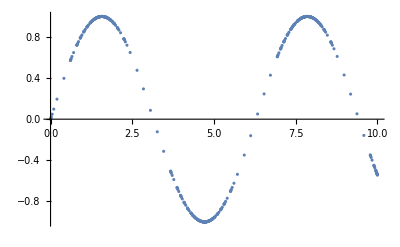

```mathematica
ListPlot[data]
```